# SM RGEs at two-loops

## Initial values at 10^3

Initial scale

```mathematica
Λini=N[Log10[173.34]]; (* 3; *)
```

By using the initial conditions from Table 3 of https://arxiv.org/pdf/1307.3536.pdf at Mtop

```mathematica
If[Λini==3,
g10=0.46;g20=0.64;g30=1.09; (*√(5/3) already included *)
Yu330=0.85;
λ0=2*0.1;
,
g10=N[√(5/3)0.35830];g20=0.64779;g30=1.1666;
Yu330=0.94018;
λ0=2*0.12604;
]
```

## Call SARAH output

```mathematica
SM=True;
If[SM,
<< SARAH/Output/SM/RGEs/RunRGEs.m
,
<< SARAH/Output/B-L-DM/RGEs/RunRGEs.m
]
```

## Try general solution (1-loop)

For standard model works well

```mathematica
rg1=RunRGEs[{g1->g10,g2->g20,g3->g30,Yu[3,3]->Yu330,λ->λ0},Λini,17,TwoLoop->True][[1]];
```

## Plots

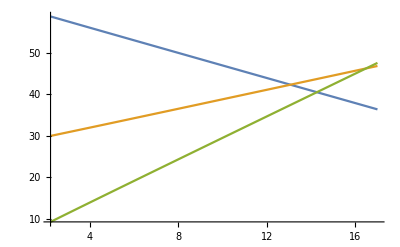

```mathematica
Plot[{(4π/(g1[t])^2)/.rg1,(4π/g2[t]^2)/.rg1,(4π/g3[t]^2)/.rg1},{t,Λini,17}]
```

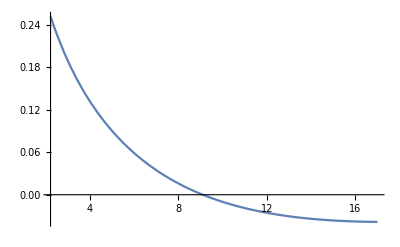

```mathematica
Plot[λ[t]/.rg1,{t,Λini,17}]
```

Check value at one point:

```mathematica
λ[Λini]/.rg1
```

0.2

```mathematica
λ[3]/.rg1
```

0.2

```mathematica
λ[3.02]/.rg1
```

0.198717

```mathematica
Yu[3,3][3]/.rg1
```

0.858913

## Appendix

Three-level relations

```mathematica
G=1.1663787*10^-5;
Subscript[M, h]=126;
```

```mathematica
λ0=G/(√2)Subscript[M, h]^2
```

0.130938